```mathematica
NS["finite_sampling_bullshit", "C:\\Users\\pglpm\\repositories\\neurobayes"]
```

```mathematica
(* article's data *)
```

```mathematica
d1={5,10,5,20,10,10,5,5,20,10}
```

{5,10,5,20,10,10,5,5,20,10}

```mathematica
Total@d1
```

100

```mathematica
d2={10,5,5,0,5,2,2,15,15,5}
```

{10,5,5,0,5,2,2,15,15,5}

```mathematica
Total@d2
```

64

```mathematica
(* test data *)
```

```mathematica
xlogy[x_,y_]:=If[x==0,0,x*Log[x/y]];SetAttributes[xlogy,Listable]
```

```mathematica
ss=10; rr=2;sss=Range[1,ss];rrr=Range[1,rr];
n=20;
```

```mathematica
f1=Table[1,ss]/ss;
f2=Table[1,ss]/ss;
```

```mathematica
SeedRandom[667]
```

```mathematica
{s1=RandomChoice[f1->sss,n],
s2=RandomChoice[f2->sss,n]}
```

{{6,10,3,1,10,4,10,6,6,1,5,6,8,4,6,3,1,2,5,4},{9,9,9,8,3,1,3,8,1,2,7,1,8,1,7,7,2,6,6,6}}

```mathematica
{sf1=(Count[s1,#]&/@sss)/n,
sf2=(Count[s2,#]&/@sss)/n}
```

{{3/20,1/20,1/10,3/20,1/10,1/4,0,1/20,0,3/20},{1/5,1/10,1/10,0,0,3/20,3/20,3/20,3/20,0}}

```mathematica
max=Max[sf1,sf2];
```

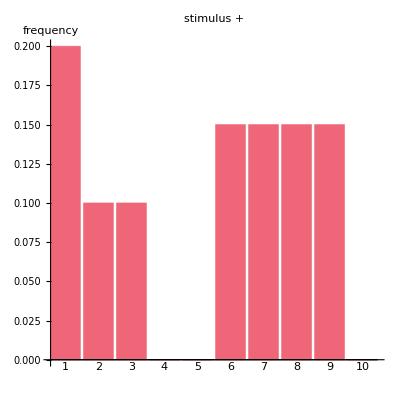

```mathematica
plot1=BarChart[sf1,Axes->True,Frame->None,PlotRange->{All,max},ChartBaseStyle->Directive[blue],ChartLabels->Range[1,ss], AxesLabel->{None,frequency},PlotLabel->"stimulus −",AspectRatio->1];

plot2=BarChart[sf2,Axes->True,Frame->None,ChartBaseStyle->Directive[red,EdgeForm[dashed]],PlotRange->{All,max},ChartLabels->Range[1,ss], AxesLabel->{None,frequency},PlotLabel->"stimulus +",AspectRatio->1]
```

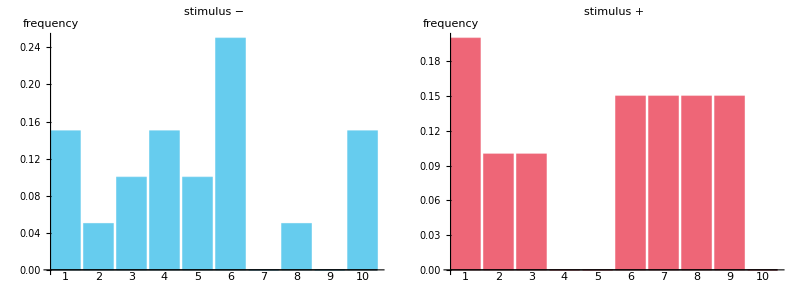

```mathematica
Grid[{{plot1,plot2}}]
```

```mathematica
expng["samples",%]
```

samples.png

```mathematica
ql1=Table[Unique["qa"],ss]
```

{qa13,qa14,qa15,qa16,qa17,qa18,qa19,qa20,qa21,qa22}

```mathematica
ql2=Table[Unique["qb"],ss]
```

{qb23,qb24,qb25,qb26,qb27,qb28,qb29,qb30,qb31,qb32}

```mathematica
(* pre-data probability for the two conditional frequencies *)
ClearAll[p0];p0[q1_,q2_]:=1;
```

```mathematica
(* probability for long-run frequencies *)
numerator[q1_,q2_]:=
Exp[n*Total[sf1*Log[q1]+sf2*Log[q2]]]*p0[q1,q2]
```

```mathematica
z=Integrate[FS[Evaluate[numerator[ql1,ql2]]]*DiracDelta[Total@ql1-1]*DiracDelta[Total@ql2-1],Sequence@@({#,0,1}&/@ql1),Sequence@@({#,0,1}&/@ql2)]
```

$Aborted

```mathematica
(* use gamma integral for uniform pre-data prob *)
gammai[vv1_,vv2_]:=((Times@@Gamma[vv1+1])/Gamma[Total[vv1+1]])*((Times@@Gamma[vv2+1])/Gamma[Total[vv2+1]])
```

```mathematica
(* use gamma integral for uniform pre-data prob *)
z= gammai[n*sf1,n*sf2];z//N
```

1.65004×10^-52

```mathematica
pp[q1_,q2_]:=numerator[q1,q2]/z
```

```mathematica
(* probability vector conditional on 1 *)
v1=Table[Module[{zv},
zv=Table[0,ss];zv[[iii]]=zv[[iii]]+1;
gammai[n*sf1+zv,n*sf2]]/z
,{iii,1,ss}];
v1//N
```

{0.133333,0.0666667,0.1,0.133333,0.1,0.2,0.0333333,0.0666667,0.0333333,0.133333}

```mathematica
Total@v1
```

1

```mathematica
v2=Table[Module[{zv},
zv=Table[0,ss];zv[[iii]]=zv[[iii]]+1;
gammai[n*sf1,n*sf2+zv]]/z
,{iii,1,ss}];
v2//N
```

{0.166667,0.1,0.1,0.0333333,0.0333333,0.133333,0.133333,0.133333,0.133333,0.0333333}

```mathematica
Total@v2
```

1

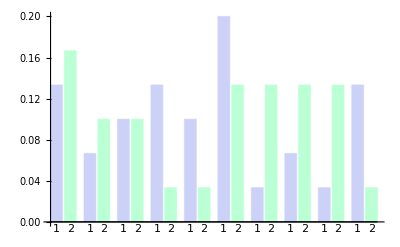

```mathematica
BarChart[T@{v1,v2},Axes->True,Frame->None,ChartLabels->{1,2}]
```

```mathematica
jointp={v1,v2}/2;
indjointp={Total[jointp],Total[jointp]}/2;
```

```mathematica
Total@Flatten@indjointp
```

1

```mathematica
mi1=Total@Flatten[jointp*Log[jointp/indjointp]];
mi1//N
```

0.0845941

```mathematica
(* post-data distribution with uniform pre-data credibilities *)nsamples=5000;unit=Table[1,nsamples];
SeedRandom[999];

fsamples1=Append[#,1-Total@#]&/@RandomVariate[DirichletDistribution[Table[1,ss]],nsamples];
fsamples2=Append[#,1-Total@#]&/@RandomVariate[DirichletDistribution[Table[1,ss]],nsamples];

rat=Block[{Indeterminate=0},Table[n*Total[sf1*Log[10,fsamples1[[iii]]]+sf2*Log[10,fsamples2[[iii]]]]
,{iii,nsamples}]];

misamples=Table[Module[{jointp,indjointp},
jointp={fsamples1[[iii]],fsamples2[[iii]]}/2;
indjointp={Total[jointp],Total[jointp]}/2;
Total@Flatten[xlogy[jointp,indjointp]]],{iii,nsamples}];
```

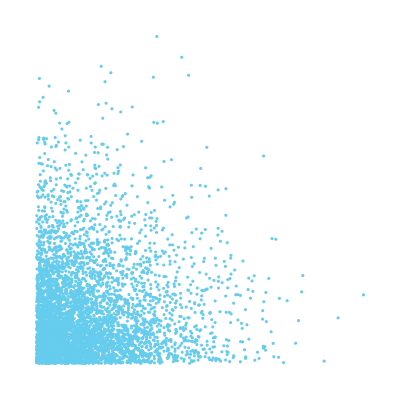

```mathematica
ListPlot[T@{fsamples1[[;;;;Round[nsamples/nsamples],1]],fsamples2[[;;;;Round[nsamples/nsamples],1]]},AspectRatio->1,PlotRange->All,FrameLabel->{Subscript[Superscript[f,"−"],1],Subscript[Superscript[f,"+"],1]}]
```

```mathematica
expng["A_sample_f1",%]
```

A_sample_f1.png

```mathematica
lpunif=n*Total[sf1*Log[10,f1]+sf2*Log[10,f2]]
```

-40

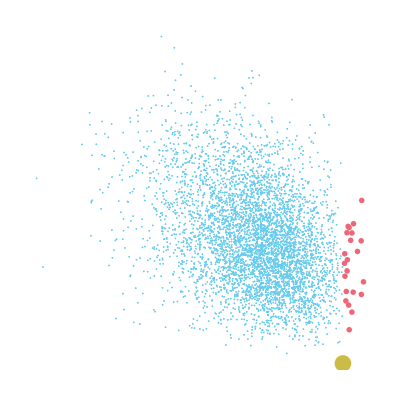

```mathematica
ListPlot[Table[Style[{rat[[ii]],misamples[[ii]]/Log[2]},If[rat[[ii]]<lpunif,blue,Sequence@@{red,PointSize[0.01]}]],{ii,nsamples}]
,PlotRange->All,AspectRatio->1,FrameLabel->{Subscript[log,10]["p"[data|"sampled freq"]],"mutual info(sampled  freq)/bit"},Epilog->{yellow,PointSize[0.03],Point[{n*Total[sf1*Log[10,f1]+sf2*Log[10,f2]],0}]}]
```

```mathematica
expng["A_init_scatter",%]
```

A_init_scatter.png

```mathematica
(* post-data distribution with uniform pre-data credibilities *)nsamples=5000;unit=Table[1,nsamples];
SeedRandom[999];

fsamples1=RandomVariate[DirichletDistribution[n*sf1+1],nsamples];
fsamples1=Append[#,1-Total@#]&/@fsamples1;
fsamples2=RandomVariate[DirichletDistribution[n*sf2+1],nsamples];
fsamples2=Append[#,1-Total@#]&/@fsamples2;

rat=Block[{Indeterminate=0},Table[n*Total[sf1*Log[10,fsamples1[[iii]]/f1]+sf2*Log[10,fsamples2[[iii]]/f2]]
,{iii,nsamples}]];

misamples=Table[Module[{jointp,indjointp},
jointp={fsamples1[[iii]],fsamples2[[iii]]}/2;
indjointp={Total[jointp],Total[jointp]}/2;
Total@Flatten[xlogy[jointp,indjointp]]],{iii,nsamples}];
```

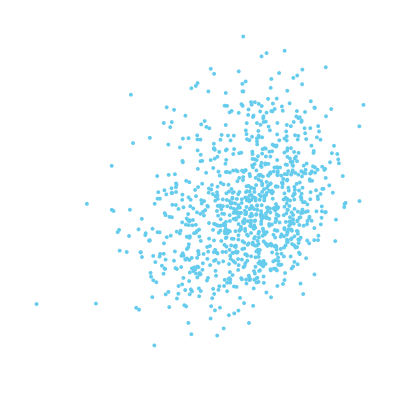

```mathematica
ListPlot[(T@{rat,misamples/Log[2]})[[;;;;Round[nsamples/1000]]],PlotRange->All,AspectRatio->1,FrameLabel->{Subscript[log,10][p[data]/p[data|uniform]],"mutual info/bit"}]
```

```mathematica
expng["A_typical_freqs_histogram",%]
```

A_typical_freqs_histogram.png

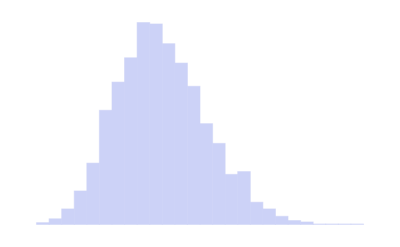

```mathematica
Histogram[misamples/Log[2],"Knuth","PDF",FrameLabel->{"mutual info/bit","p"["mutual  info"]}]
```

```mathematica
expng["A_mutualinfo_hist",%]
```

A_mutualinfo_hist.png

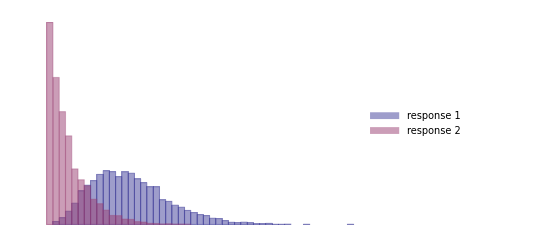

```mathematica
Histogram[{fsamples1[[;;,4]],fsamples2[[;;,4]]},"Knuth","PDF",FrameLabel->{"frequency of state #4","p"[frequency]},ChartLegends->Placed[{"response 1","response 2"},{{0.9,0.9}}]]
```

```mathematica
expng["A_freq4_hist",%]
```

A_freq4_hist.png

```mathematica
{me1=Mean@fsamples1,me2=Mean@fsamples2}//MF
```

(0.132959 | 0.0669621 | 0.101733 | 0.132584 | 0.0998356 | 0.199927 | 0.0333746 | 0.0662526 | 0.0330695 | 0.133303
0.166234 | 0.0995195 | 0.100363 | 0.033344 | 0.0340277 | 0.132723 | 0.133386 | 0.133655 | 0.133921 | 0.032827)

```mathematica
prfromunif=Times@@(f1^(n*sf1)*f2^(n*sf2))
```

1/10000000000000000000000000000000000000000

```mathematica
prfrommean=Times@@(me1^(n*sf1)*me2^(n*sf2))
```

4.59769×10^-36

```mathematica
prfrommean/prfromunif
```

45976.9

```mathematica
rat=Times@@((me1/f1)^(n*sf1)*(me2/f2)^(n*sf2))
```

45976.9

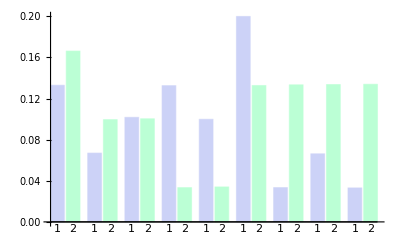

```mathematica
BarChart[T@{Mean@fsamples1,Mean@fsamples2},Axes->True,Frame->None,ChartLabels->{1,2}]
```

```mathematica
mjointp={Mean@fsamples1,Mean@fsamples2}/2;
mindjointp={Total[mjointp],Total[mjointp]}/2;
Total@Flatten[mjointp*Log[mjointp/mindjointp]]
```

0.0684525

```mathematica
mjointp={Exp@Mean@Log@fsamples1,Exp@Mean@Log@fsamples2}/2;
mindjointp={Total[mjointp],Total[mjointp]}/2;
Total@Flatten[mjointp*Log[mjointp/mindjointp]]
```

0.0851198

```mathematica
Map[Append[#,1-Total@#]&,RandomVariate[DirichletDistribution[Table[1,3]],5],1]
```

{{0.0401865,0.0630454,0.896768},{0.056915,0.753103,0.189982},{0.351492,0.564079,0.0844293},{0.536968,0.2443,0.218732},{0.197278,0.219246,0.583476}}

```mathematica
(* post-data distribution with non-uniform pre-data credibilities *)Block[{ss=2},
nsamples=500;si=100;unit=Table[1,nsamples];
SeedRandom[999];

paramsamples=Map[Append[#,1-Total@#]&,RandomVariate[DirichletDistribution[Table[1,ss]],nsamples],1];


fsamples1=Table[Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[si*paramsamples[[iii]]],1]]
,{iii,nsamples}];

fsamples2=Table[Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[si*paramsamples[[iii]]],1]]
,{iii,nsamples}];]
```

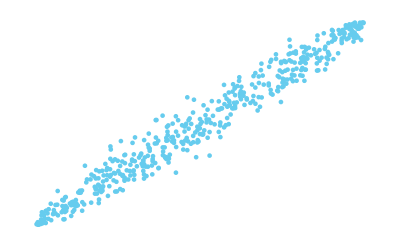

```mathematica
ListPlot[T@{fsamples1[[;;,1]],fsamples2[[;;,1]]}]
```

```mathematica
fsamples2
```

{{0.889982,0.110018},{0.0171795,0.982821},{0.602125,0.397875},{0.862838,0.137162},{0.849587,0.150413}}

```mathematica
(* post-data distribution with non-uniform pre-data credibilities *)nsamples=5000;si=1000;unit=Table[1,nsamples];
SeedRandom[995];

paramsamples=Map[Append[#,1-Total@#]&,RandomVariate[DirichletDistribution[Table[10,ss]],nsamples],1];


fsamples1=Table[Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[si*paramsamples[[iii]]],1]]
,{iii,nsamples}];

fsamples2=Table[Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[si*paramsamples[[iii]]],1]]
,{iii,nsamples}];

rat=Block[{Indeterminate=0},Table[n*Total[sf1*Log[10,fsamples1[[iii]]]+sf2*Log[10,fsamples2[[iii]]]]
,{iii,nsamples}]];

misamples=Table[Module[{jointp,indjointp},
jointp={fsamples1[[iii]],fsamples2[[iii]]}/2;
indjointp={Total[jointp],Total[jointp]}/2;
Total@Flatten[xlogy[jointp,indjointp]]],{iii,nsamples}];
```

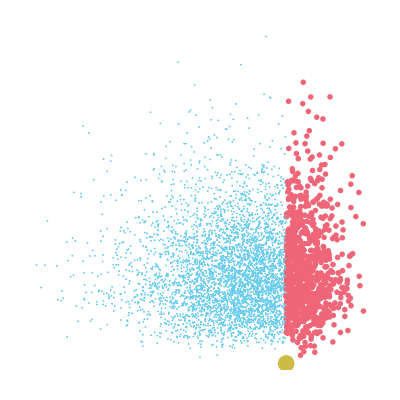

```mathematica
ListPlot[Table[Style[{rat[[ii]],misamples[[ii]]/Log[2]},If[rat[[ii]]<lpunif,blue,Sequence@@{red,PointSize[0.01]}]],{ii,nsamples}]
,PlotRange->{All,All},AspectRatio->1,FrameLabel->{Subscript[log,10]["p"[data|"sampled freq"]],"mutual info(sampled  freq)/bit"},Epilog->{yellow,PointSize[0.03],Point[{n*Total[sf1*Log[10,f1]+sf2*Log[10,f2]],0}]}]
```

```mathematica
expng["B_init_scatter",%]
```

B_init_scatter.png

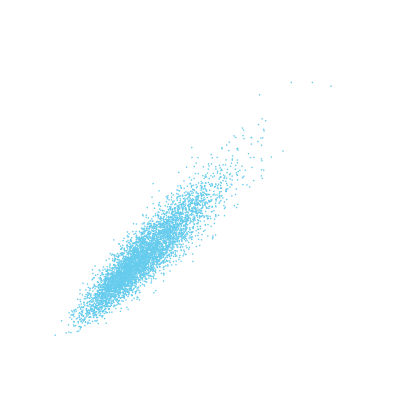

```mathematica
ListPlot[T@{fsamples1[[;;;;Round[nsamples/nsamples],1]],fsamples2[[;;;;Round[nsamples/nsamples],1]]},AspectRatio->1,PlotRange->{{0,0.3},{0,0.3}},FrameLabel->{Subscript[Superscript[f,"−"],1],Subscript[Superscript[f,"+"],1]}]
```

```mathematica
expng["B_sample_f1",%]
```

B_sample_f1.png

```mathematica
(* post-data distribution with non-uniform pre-data credibilities *)nsamples=5000;
si=1000;
unit=Table[1,nsamples];
SeedRandom[995];

paramsamples=Map[Append[#,1-Total@#]&,RandomVariate[DirichletDistribution[Table[10,ss]],nsamples],1];


fsamples1=Table[Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[n*sf1+si*paramsamples[[iii]]],1]]
,{iii,nsamples}];

fsamples2=Table[Append[#,1-Total@#]&@Flatten[RandomVariate[DirichletDistribution[n*sf2+si*paramsamples[[iii]]],1]]
,{iii,nsamples}];

rat=Block[{Indeterminate=0},Table[n*Total[sf1*Log[10,fsamples1[[iii]]]+sf2*Log[10,fsamples2[[iii]]]]
,{iii,nsamples}]];

misamples=Table[Module[{jointp,indjointp},
jointp={fsamples1[[iii]],fsamples2[[iii]]}/2;
indjointp={Total[jointp],Total[jointp]}/2;
Total@Flatten[xlogy[jointp,indjointp]]],{iii,nsamples}];
```

```mathematica
expng["B_typical_freqs_histogram",%]
```

B_typical_freqs_histogram.png

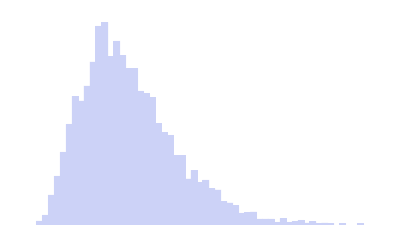

```mathematica
Histogram[misamples/Log[2],"Knuth","PDF",FrameLabel->{"mutual info/bit","p"["mutual  info"]}]
```

```mathematica
expng["B_mutualinfo_hist",%]
```

B_mutualinfo_hist.png

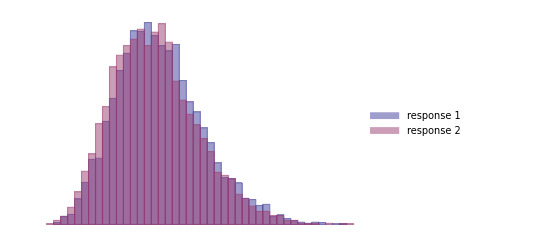

```mathematica
Histogram[{fsamples1[[;;,4]],fsamples2[[;;,4]]},"Knuth","PDF",FrameLabel->{"frequency of state #4","p"[frequency]},ChartLegends->Placed[{"response 1","response 2"},{{0.9,0.9}}]]
```

```mathematica
expng["B_freq4_hist",%]
```

B_freq4_hist.png

```mathematica
(* probability distribution of mutual information for limit frequency *)
```

```mathematica
(* find expected value for update *)

samplesmi=Table[Module[{s1,s2,sf1,sf2,z,v1,v2,jointp,indjointp},
{s1=RandomChoice[f1->sss,n],
s2=RandomChoice[f2->sss,n]};

{sf1=(Count[s1,#]&/@sss)/n,
sf2=(Count[s2,#]&/@sss)/n};

z= gammai[n*sf1,n*sf2];

v1=Table[Module[{zv},
zv=Table[0,ss];zv[[iii]]=zv[[iii]]+1;
gammai[n*sf1+zv,n*sf2]]/z
,{iii,1,ss}];

v2=Table[Module[{zv},
zv=Table[0,ss];zv[[iii]]=zv[[iii]]+1;
gammai[n*sf1,n*sf2+zv]]/z
,{iii,1,ss}];

jointp={v1,v2}/2;
indjointp={Total[jointp],Total[jointp]}/2;

Total@Flatten[jointp*Log[jointp/indjointp]]]
,1000];
```

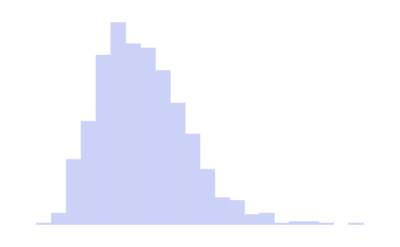

```mathematica
Histogram[samplesmi/Log[2],"FreedmanDiaconis",PDF]
```

```mathematica
Mean@samplesmi//N
```

0.0496683

```mathematica
%/Log[2]
```

0.0716562

```mathematica
BernoulliDistribution
```

```mathematica
(* conditional probabilities for next observation, conditional on data above *)
```